# Script for IRS vs BoB comparison 1:1 Mass ratio

## to accompany https://arxiv.org/abs/2205.14742

Author: Maria Babiuc-Hamilton and Dillon Buskirk

```mathematica
ClearAll["Global`*"];Off[General::spell];Remove["Global`*"]
SetOptions[Simplify,TimeConstraint->1000];
$Assumptions=η>0 &&t∈Reals;
Unprotect[Sqrt]; Sqrt[x_^2]:=x; Protect[Sqrt];
$MinPrecision=$MachinePrecision; (* $MachinePrecision;*)
```

Initial and final parameters

From FinalSpinMassQNM.nb,  values for equal non-spinning binaries χf0Meq and Mfχ0Meq

```mathematica
χf=0.686526691452522(*mean final spin for nonspinning individual BSs in the binary *)
```

0.686527

```mathematica
Mf=0.95158896875(*mean final mass for nonspinning individual BSs in the binary *)
```

0.951589

Our fit: the mean value for equal non-spinning binaries from FinalSpinMassQNM.nb,  for l=2, m=2 mode:

```mathematica
MfωQNM =0.5422370151014632
QQNM=3.300909722911351
ωQNM=MfωQNM/Mf
τ = 2 QQNM/ωQNM(*15.144152677226*)
```

0.542237

3.30091

0.569823

11.5857

McWilliams fits

```mathematica
MωISCOW=(-0.091933*χf+0.097593)/(χf^2-2.4228*χf+1.4366)
MωQNMW=1.5251-1.1568*(1-χf)^0.1292
```

0.140958

0.529311

PN fits

```mathematica
rISCO = 3.45425
```

3.45425

```mathematica
MωISCO = Simplify[1/(rISCO^(3/2)+χf)]
```

0.140717

Freely chosen parameters

```mathematica
Ap=1;R=1;tp=0;
```

Starting BOB formulation

take the initial values from the i3PN nspiral for ti = tISCO = tLR

Values taken directly from EccInsMerger_q1e0001. For this spin, rISCO=3.45425.

```mathematica
Ω3OrbPNISCO = 0.075297 ;
Ω3OrbPNISCOdot = 8.57723 10^-4 ;
```

Now we can implement the BoB

```mathematica
Ωi =MωISCOW/Mf;
Ωidot = Ω3OrbPNISCOdot;
tp =0;
ΩQNM=ωQNM/2
ti=tp-τ/2 Log[(ΩQNM^4-Ωi^4)/(2*τ*Ωi^3 Ωidot)-1]
```

0.284911

-26.291

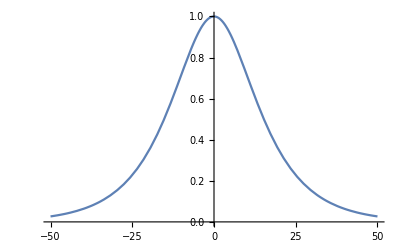

```mathematica
Ap=1;(*1.068*(1-Mf)^0.8918;*)
ψ4[t_]:=Ap*Sech[(t-tp)/τ];
Plot[ψ4[t],{t,-50,50}]
```

```mathematica
kB=((ΩQNM^4-Ωi^4)/(1-Tanh[(ti-tp)/τ]))
```

0.00308656

```mathematica
ΩB[t_]:=(Ωi^4+kB(Tanh[(t-tp)/τ]-Tanh[(ti-tp)/τ]))^(1/4)
```

```mathematica
ωBoB[t_]:=2*ΩB[t];
```

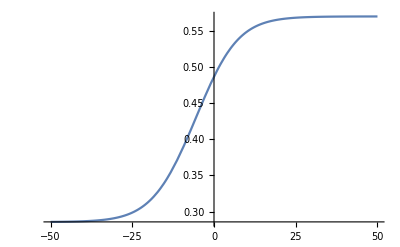

```mathematica
Plot[ωBoB[t],{t,-50,50}]
```

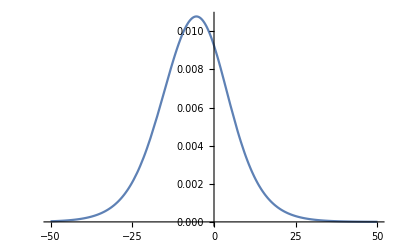

```mathematica
Plot[ωBoB'[t],{t,-50,50}]
```

```mathematica
Kappap=(Ωi^4+kB(1-Tanh[(ti-tp)/τ]))^(1/4)
```

0.284911

```mathematica
Kappam=(Ωi^4-kB(1+Tanh[(ti-tp)/τ]))^(1/4)
```

0.142829

```mathematica
arctanp[t_]:=Kappap*τ*(ArcTan[(ΩB[t]/Kappap)]-ArcTan[Ωi/Kappap])
arctanm[t_]:=Kappam*τ*(ArcTan[ΩB[t]/Kappam]-ArcTan[Ωi/Kappam])
arctanhp[t_]:=Kappap*τ*(ArcTanh[ΩB[t]/Kappap]-ArcTanh[Ωi/Kappap])
arctanhm[t_]:=Kappam*τ*(ArcTanh[ΩB[t]/Kappam]-ArcTanh[Ωi/Kappam])
```

```mathematica
PhaseB[t_]:=arctanp[t]+arctanhp[t]-arctanm[t]-arctanhm[t]
```

```mathematica
ϕBoB[t_]:=2*PhaseB[t]
```

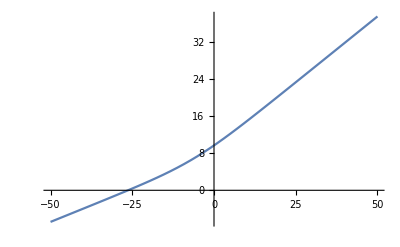

```mathematica
Plot[ϕBoB[t],{t,-50,50}]
```

```mathematica
AmpBoB[t_]:=ψ4[t]/ωBoB[t]^2
```

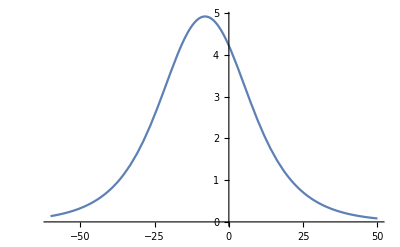

```mathematica
Plot[AmpBoB[t],{t,-60,50}]
```

```mathematica
MaxAmpBoB=FindMaxValue[{AmpBoB[t],-40<=t<=0},{t,-20}]
```

4.92249

```mathematica
tpBoB = First@FindArgMax[{AmpBoB[t],-40<=t<=0},{t,-20}]
```

-8.00028

```mathematica
hBoB[t_]:=-AmpBoB[t]*Exp[-ⅈ* ϕBoB[t]]
```

Note that the maximum in amplitude and maximum in the rate of variation of the frequency is not the same!

```mathematica
Plot[ωBoB'[t],{t,-50,50}]
```

-Graphics-

```mathematica
tfBoB=t/.FindRoot[ωBoB''[t]==0,{t,-20,10}]
```

-5.39017

Now we implement the IRS

```mathematica
m1 =0.5; m2=1-m1;
q=m1/m2; M=m1+m2; μ=(m1*m2)/M;η=μ/M;
```

Check the initial frequency, quality factor and damping time against the numerical fit

```mathematica
sfn=χf
ωqnm=1-0.63(1-sfn)^0.3
```

0.686527

0.555163

```mathematica
ScientificForm[MeanDeviation[{ωqnm,ωQNM}]]
```

7.32977×10^-3

```mathematica
Q=2/(1-sfn)^0.45;
```

```mathematica
ScientificForm[MeanDeviation[{Q,QQNM}]]
```

3.49714×10^-2

```mathematica
b=N[16014/979-29132/1343 η^2]
```

15.0018

1107.1181 takes b = τ

Will use ωQNM, τ  and QQNM for consistency

```mathematica
c=N[206/903+180/1141 η^(1/2)+424/1205*η^2/Log[η]]
kI=N[713/1056-23/193 η]
α=N[1/QQNM^2(16313/562+21345/124 η)]
```

0.291143

0.645397

6.61352

```mathematica
fs[t_]:=c/2(1+1/kI)^(1+kI)(1-(1+1/kI ⅇ^((-2*t)/τ))^-kI);
fs2=Simplify[fs[t]^2, Assumptions->{η>0}];fs4=Simplify[fs2^2];
fsdot=Simplify[D[fs[t],t]];
```

```mathematica
ωIRS[t_]:=ωQNM*(1-fs[t])
```

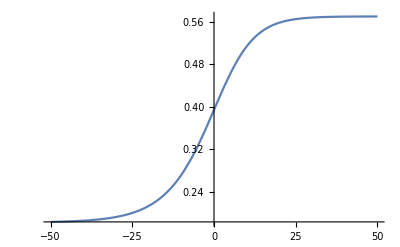

```mathematica
Plot[ωIRS[t],{t,-50,50}]
```

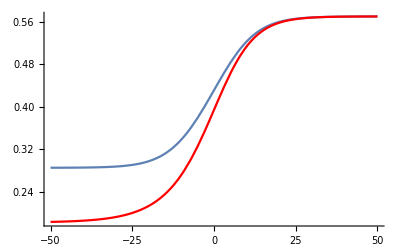

```mathematica
Show[Plot[ωBoB[t+tfBoB],{t,-50,50}],
Plot[ωIRS[t],{t,-50,50},PlotStyle->Red], Axes->True,AxesOrigin->Automatic, PlotRange->{0,All}]
```

Initial values don’t match

```mathematica
ωIRS[ti]
```

0.198458

```mathematica
ωBoB[ti+tfBoB]
```

0.290005

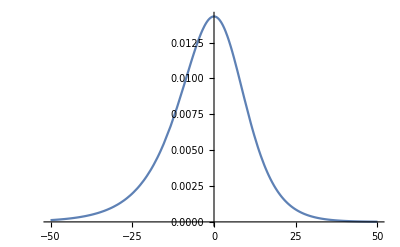

```mathematica
Plot[ωIRS'[t],{t,-50,50}]
```

```mathematica
tfIRS=t/.FindRoot[ωIRS''[t]==0,{t,-40,40}]
```

-3.39233×10^-15

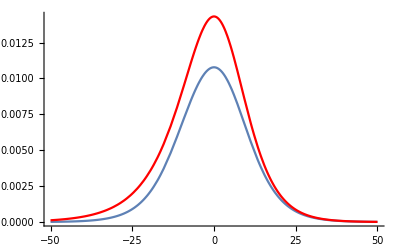

```mathematica
Show[Plot[ωBoB'[t+tfBoB],{t,-50,50}],
Plot[ωIRS'[t+tfIRS],{t,-50,50},PlotStyle->Red], Axes->True,AxesOrigin->Automatic, PlotRange->{0,All}]
```

```mathematica
ϕIRS= Integrate[ωIRS[t],t];
```

```mathematica
Δϕ= Re[ϕBoB[tfBoB]] - Simplify[ϕIRS/.{t->0}]
```

4.93233

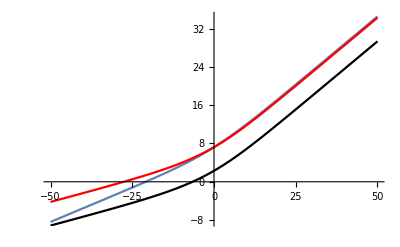

```mathematica
Show[Plot[ϕBoB[t+tfBoB],{t,-50,50}],
Plot[ϕIRS+Δϕ,{t,-50,50},PlotStyle->Red],
Plot[ϕIRS,{t,-50,50},PlotStyle->Black]]
```

```mathematica
AmpIRS[t_]:=Simplify[Ap/ωIRS[t](Abs[fsdot]/(1+α*(fs2-fs4)))^(1/2)]
```

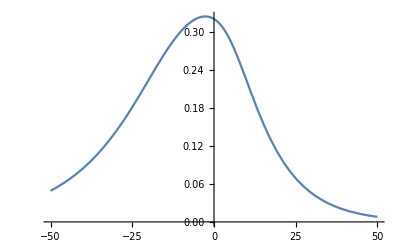

```mathematica
Plot[AmpIRS[t],{t,-50,50}]
```

```mathematica
MaxAmpIRS=FindMaxValue[{AmpIRS[t],-40<=t<=0},{t,-20}]
```

0.325076

```mathematica
tpIRS = First@FindArgMax[{AmpIRS[t],-40<=t<=0},{t,-20}]
```

-2.66924

```mathematica
Δtp = tpBoB-tpIRS
```

-5.33104

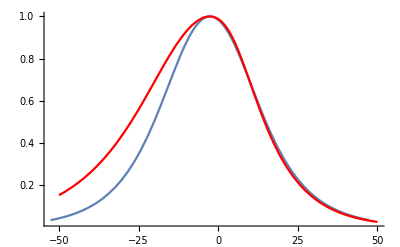

```mathematica
Show[Plot[AmpBoB[t+tfBoB]/MaxAmpBoB,{t,-50+Δtp/2,50+Δtp/2}],
Plot[AmpIRS[t]/MaxAmpIRS,{t,-50,50},PlotStyle->Red],
PlotRange->All]
```

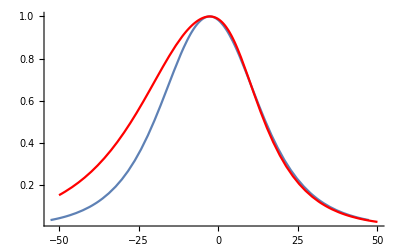

```mathematica
Show[Plot[AmpBoB[t+Δtp]/MaxAmpBoB,{t,-50+Δtp/2,50+Δtp/2}],
Plot[AmpIRS[t]/MaxAmpIRS,{t,-50,50},PlotStyle->Red],
PlotRange->All]
```

```mathematica
hIRS[t_]:=AmpIRS[t]*Exp[-ⅈ*(ϕIRS)]
```

```mathematica
hIRSΔ[t_]:=AmpIRS[t]*Exp[-ⅈ*(ϕIRS+Δϕ)]
```

Let’s build the strains

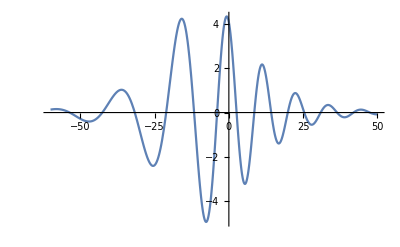

```mathematica
Plot[Re[hBoB[t]],{t,-60,50}]
```

```mathematica
MaxRehBoB = FindMaxValue[{Re[hBoB[t]],-40<=t<=-10},{t,-20}]
```

4.221

```mathematica
MinRehBoB =FindMinValue[{Re[hBoB[t]],-20<=t<=0},{t,-10}]
```

-4.92094

```mathematica
thBoB = First@FindArgMin[{Re[hBoB[t]],-20<=t<=0},{t,-10}]
```

-7.64296

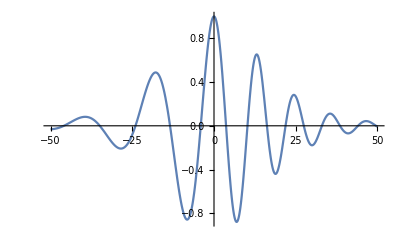

```mathematica
Plot[Re[hBoB[t+thBoB]]/MinRehBoB,{t,-50,50}]
```

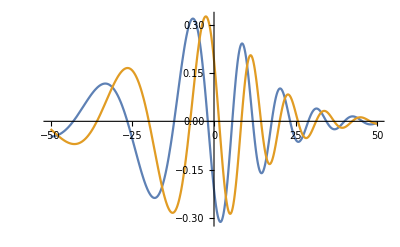

```mathematica
Plot[{Re[hIRS[t]],Re[hIRSΔ[t]]},{t,-50,50}]
```

```mathematica
MaxRehIRS = FindMaxValue[{Re[hIRS[t]],-20<=t<=0},{t,-10}]
```

0.318295

```mathematica
MinRehIRS = FindMinValue[{Re[hIRS[t]],-10<=t<=10},{t,0}]
```

-0.311749

```mathematica
MaxRehΔIRS = FindMaxValue[{Re[hIRSΔ[t]],-20<=t<=0},{t,-10}]
```

0.325061

```mathematica
MinRehΔIRS = FindMinValue[{Re[hIRSΔ[t]],-10<=t<=10},{t,0}]
```

-0.286672

```mathematica
thIRS = First@FindArgMax[{Re[hIRS[t]],-20<=t<=0},{t,-10}]
```

-6.45085

```mathematica
thΔIRS = First@FindArgMax[{Re[hIRSΔ[t]],-20<=t<=0},{t,-10}]
```

-2.50022

```mathematica
t0hIRSBoB = thBoB-thIRS
```

-1.19212

```mathematica
t0hIRSΔBoB = thBoB-thΔIRS
```

-5.14275

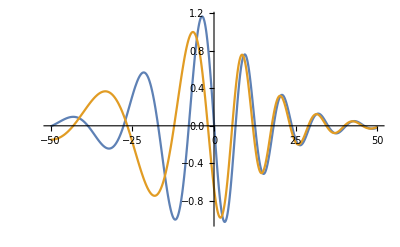

```mathematica
Plot[{-Re[hBoB[t-4]]/MaxRehBoB, Re[hIRS[t]]/MaxRehIRS},{t,-50,50}]
```

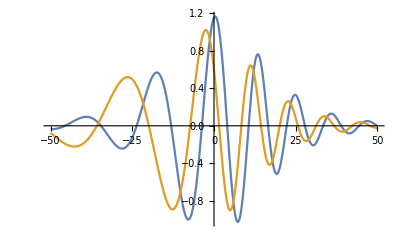

```mathematica
Plot[{-Re[hBoB[t-8]]/MaxRehBoB, Re[hIRSΔ[t]]/MaxRehIRS},{t,-50,50}]
```

```mathematica
tfBoB
```

-5.39017

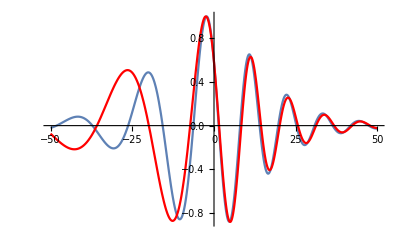

```mathematica
Show[Plot[Re[hBoB[t+tfBoB]]/MinRehBoB,{t,-50,50}],
Plot[Re[hIRSΔ[t]]/MaxRehΔIRS,{t,-50,50},PlotStyle->Red],PlotRange->All]
```

Now we upload the SXS BBH:0180 data

```mathematica
SXS0180Data=Import["/Users/babiuc/BBH0180_22.dat","Table"]
```

{{-107.532,-0.00044193,-0.00471299},{-106.3,-0.000443996,-0.0047269},19291,{9758.27,-5.64872×10^-6,-0.0000188056},{9758.37,-5.65426×10^-6,-0.0000187994}}
 |  |  |  |

```mathematica
SXS0180DataTime=SXS0180Data[[All,1]];
```

```mathematica
ReSXS0180DataStrain=SXS0180Data[[All,2]];
```

```mathematica
ImSXS0180DataStrain=SXS0180Data[[All,3]];
```

```mathematica
AmpSXS0180DataStrain = Sqrt[ReSXS0180DataStrain^2+ImSXS0180DataStrain^2];
```

```mathematica
MaxAmpSXS0180DataStrain=Max[Abs[AmpSXS0180DataStrain]]
```

0.393661

```mathematica
Position[AmpSXS0180DataStrain ,_?(#>0.999999*MaxAmpSXS0180DataStrain&)]
```

{{16930}}

```mathematica
ReSXS0180DataStrainNorm = ReSXS0180DataStrain/MaxAmpSXS0180DataStrain;
ImSXS0180DataStrainNorm = ImSXS0180DataStrain/MaxAmpSXS0180DataStrain;
```

```mathematica
SXS0180DataTimeShift=SXS0180DataTime-SXS0180DataTime[[16930]];
```

```mathematica
hpReSXS0180DataShift=Transpose[{SXS0180DataTimeShift,+ReSXS0180DataStrainNorm}];
```

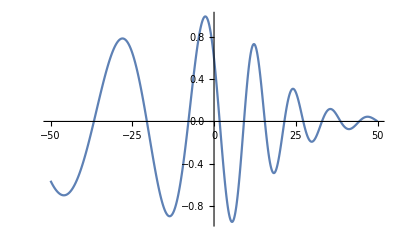

```mathematica
ListLinePlot[hpReSXS0180DataShift[[16430;;17430]]]
```

```mathematica
AmpSXS0180DataStrainNorm = AmpSXS0180DataStrain/MaxAmpSXS0180DataStrain;
```

```mathematica
AmpSXS0180DataShift=Transpose[{SXS0180DataTimeShift,AmpSXS0180DataStrainNorm }];
```

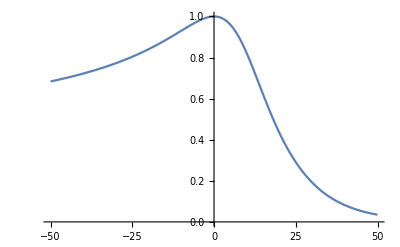

```mathematica
ListLinePlot[AmpSXS0180DataShift[[16430;;17430]]]
```

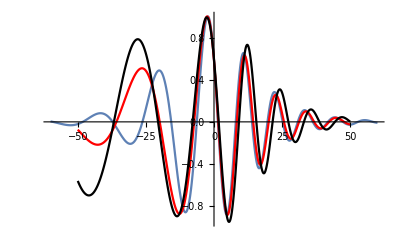

```mathematica
Show[Plot[Re[hBoB[t+tfBoB]]/MinRehBoB,{t,-60,60}],
Plot[Re[hIRSΔ[t]]/MaxRehΔIRS,{t,-50,50},PlotStyle->Red],
ListLinePlot[hpReSXS0180DataShift[[16430;;17430]],PlotStyle->Black],
PlotRange->All]
```

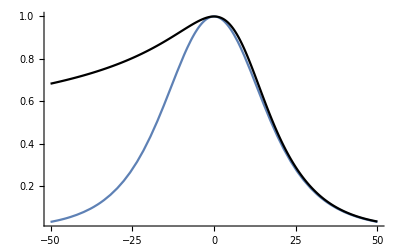

```mathematica
Show[Plot[AmpBoB[t+tpBoB]/MaxAmpBoB,{t,-50,50}],
ListLinePlot[AmpSXS0180DataShift[[16430;;17430]],PlotStyle->Black],PlotRange->All]
```

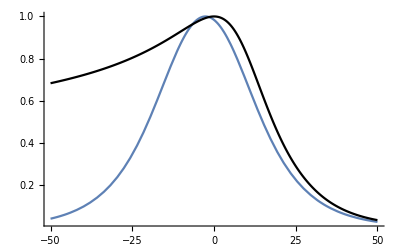

```mathematica
Show[Plot[AmpBoB[t+tfBoB]/MaxAmpBoB,{t,-50,50}],
ListLinePlot[AmpSXS0180DataShift[[16430;;17430]],PlotStyle->Black],PlotRange->All]
```

```mathematica
SXS0180DataTimeShiftIRS=SXS0180DataTime-SXS0180DataTime[[16930]] +tpIRS;
AmpSXS0180DataShiftIRS=Transpose[{SXS0180DataTimeShiftIRS,AmpSXS0180DataStrainNorm }];
```

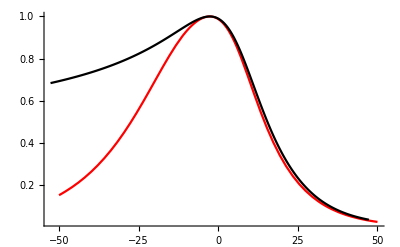

```mathematica
Show[
Plot[AmpIRS[t]/MaxAmpIRS,{t,-50,50},PlotStyle->Red],
ListLinePlot[AmpSXS0180DataShiftIRS[[16430;;17430]],PlotStyle->Black],
PlotRange->All]
```

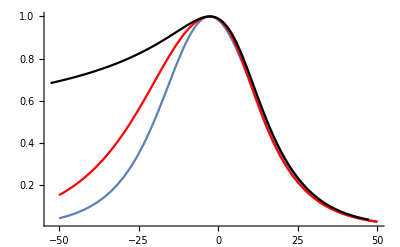

```mathematica
Show[Plot[AmpBoB[t+Δtp]/MaxAmpBoB,{t,-50,50}],
Plot[AmpIRS[t]/MaxAmpIRS,{t,-50,50},PlotStyle->Red],
ListLinePlot[AmpSXS0180DataShiftIRS[[16430;;17430]],PlotStyle->Black],PlotRange->All]
```

```mathematica
ArgSXS= Flatten[ArcTan[ImSXS0180DataStrainNorm/ReSXS0180DataStrainNorm]];
```

Function taken from https://community.wolfram.com/groups/-/m/t/1340126

```mathematica
Unwrap[lst_List]:=Unwrap[lst,2Pi] (*phase jumps of 2Pi is the default because of trigonometric funtions*)
Unwrap[lst_List,Δ_]:=Unwrap[lst,Δ,Scaled[0.5]] (*default tolerance is half the phase jump Δ*)
Unwrap[lst_List,Δ_,tolerance_]:=Module[{tol,jumps},tol=If[Head[tolerance]===Scaled,Δ tolerance[[1]],tolerance];
jumps=Differences[lst];
jumps=-Sign[jumps]Unitize[Chop[Abs[jumps],tol]];
jumps=Δ Prepend[Accumulate[jumps],0];
jumps+lst]
```

```mathematica
unwrapArgSXS=Unwrap[ArgSXS,3];
```

```mathematica
unwrapArgSXSFiltered=MeanFilter[unwrapArgSXS,100];
```

```mathematica
ϕSXS=Transpose[{SXS0180DataTimeShift,Flatten[-unwrapArgSXS]}];
```

```mathematica
ϕSXSfiltered=Transpose[{SXS0180DataTimeShift,Flatten[-unwrapArgSXSFiltered]}];
```

```mathematica
interpϕSXS=Interpolation[ϕSXS[[16430;;17430]],InterpolationOrder->4]
```

InterpolatingFunction[…]

```mathematica
interpϕSXSfiltered=Interpolation[ϕSXSfiltered[[16430;;17430]],InterpolationOrder->4]
```

InterpolatingFunction[…]

```mathematica
ΔϕSXSBoB =interpϕSXS[0]-Re[ϕBoB[tfBoB]]
```

332.711

InterpolatingFunction::dmval: Input value {-49.998} lies outside the range of data in the interpolating function. Extrapolation will be used.

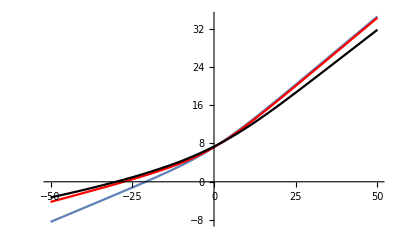

```mathematica
Show[Plot[ϕBoB[t+tfBoB],{t,-50,50}],
Plot[ϕIRS+Δϕ,{t,-50,50},PlotStyle->Red],
Plot[interpϕSXSfiltered[t]-ΔϕSXSBoB,{t,-50,50},PlotStyle->Black],
PlotRange->All]
```

```mathematica
interpωSXSfiltered[t_]:=interpϕSXSfiltered'[t]
```

```mathematica
interpωSXSfiltered[0]
```

0.342879

InterpolatingFunction::dmval: Input value {-49.998} lies outside the range of data in the interpolating function. Extrapolation will be used.

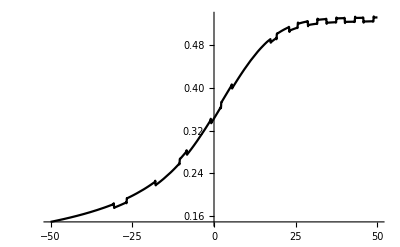

```mathematica
Plot[interpωSXSfiltered[t],{t,-50,50},PlotStyle->Black]
```

InterpolatingFunction::dmval: Input value {-49.998} lies outside the range of data in the interpolating function. Extrapolation will be used.

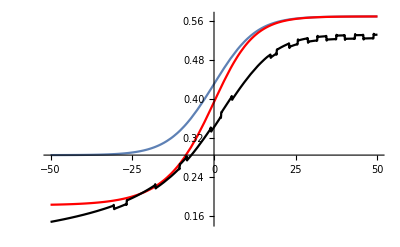

```mathematica
Show[Plot[ωBoB[t+tfBoB],{t,-50,50}],
Plot[ωIRS[t],{t,-50,50},PlotStyle->Red],
Plot[interpωSXSfiltered[t],{t,-50,50},PlotStyle->Black],
PlotRange->All]
```

InterpolatingFunction::dmval: Input value {-49.998} lies outside the range of data in the interpolating function. Extrapolation will be used.

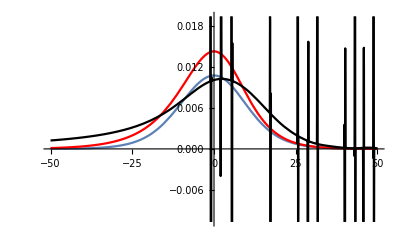

```mathematica
Show[Plot[ωBoB'[t+tfBoB],{t,-50,50}],
Plot[ωIRS'[t],{t,-50,50},PlotStyle->Red],
Plot[interpωSXSfiltered'[t],{t,-50,50},PlotStyle->Black],
PlotRange->All]
```

New plot for paper: phase for IRS-BoB comparison

For the standard deviation plot

```mathematica
(*dataBoBr=Re[hBoB[t-trBoB/2]]/MaxAmpBoB;
dataBoB0=Re[hBoB[t-Δt0/2]]/MaxAmpBoB;
dataIRS=Re[hIRSΔ[t]]/MaxAmpIRS;
datamIRS=Re[-hIRS[t]]/MaxAmpIRS;
datamIRSΔ=Re[-hIRSΔ[t]]/MaxAmpIRS;*)
```

## Below is Tabulating for Python Plots

```mathematica
dt=0.01;
```

```mathematica
tArray=Table[t,{t,-50,50,dt}];
```

```mathematica
(*ωBoBTab=Table[ωBoB[t-Δtp/2],{t,-50,50,dt}];*)
```

```mathematica
(*ωIRSTab=Table[ωIRS[t],{t,-50,50,dt}];*)
```

```mathematica
(*ωBoBvsTimeTab=Partition[Riffle[tArray,ωBoBTab],2];*)
```

```mathematica
(*PrependTo[ωBoBvsTimeTab, {"t(M)", "ω(t)"}];*)
```

```mathematica
(*ωIRSvsTimeTab=Partition[Riffle[tArray,ωIRSTab],2];*)
```

```mathematica
(*PrependTo[ωIRSvsTimeTab, {"t(M)", "ω(t)"}];*)
```

```mathematica
ϕBoBTab=Table[ϕBoB[t+tfBoB],{t,-50,50,dt}];
```

```mathematica
ϕIRSTab=Table[ϕIRS+Δϕ,{t,-50,50,dt}];
```

```mathematica
ϕBoBvsTimeTab=Partition[Riffle[tArray,ϕBoBTab],2];
```

```mathematica
PrependTo[ϕBoBvsTimeTab, {"t(M)", "ϕ(t)"}];
```

```mathematica
ϕIRSvsTimeTab=Partition[Riffle[tArray,ϕIRSTab],2];
```

```mathematica
PrependTo[ϕIRSvsTimeTab, {"t(M)", "ϕ(t)"}];
```

```mathematica
hBoBTab=Table[Re[hBoB[t+tfBoB]]/MaxAmpBoB,{t,-50,50,dt}];
```

```mathematica
hIRSTab=Table[Re[hIRSΔ[t]]/MaxAmpIRS,{t,-50,50,dt}];
```

```mathematica
hBoBvsTimeTab=Partition[Riffle[tArray,hBoBTab],2];
```

```mathematica
PrependTo[hBoBvsTimeTab, {"t(M)", "h(t)"}];
```

```mathematica
hIRSvsTimeTab=Partition[Riffle[tArray,hIRSTab],2];
```

```mathematica
PrependTo[hIRSvsTimeTab, {"t(M)", "h(t)"}];
```

```mathematica
(*AmpBoBTab=Table[AmpBoB[t-Δtp]/MaxAmpBoB,{t,-50,50,dt}];*)
```

```mathematica
(*AmpIRSTab=Table[AmpIRS[t]/MaxAmpIRS,{t,-50,50,dt}];*)
```

```mathematica
(*AmpBoBvsTimeTab=Partition[Riffle[tArray,AmpBoBTab],2];*)
```

```mathematica
(*PrependTo[AmpBoBvsTimeTab, {"t(M)", "hAmp(t)"}];*)
```

```mathematica
(*AmpIRSvsTimeTab=Partition[Riffle[tArray,AmpIRSTab],2];*)
```

```mathematica
(*PrependTo[AmpIRSvsTimeTab, {"t(M)", "hAmp(t)"}];*)
```

```mathematica
(*Export["dropbox/dillon/paperplottingwork/wBoB.txt", ωBoBvsTimeTab]*)
```

```mathematica
(*Export["dropbox/dillon/paperplottingwork/wIRS.txt", ωIRSvsTimeTab]*)
```

```mathematica
Export["dropbox/dillon/paperplottingwork/phiBoB.txt", ϕBoBvsTimeTab]
```

dropbox/dillon/paperplottingwork/phiBoB.txt

```mathematica
Export["dropbox/dillon/paperplottingwork/phiIRS.txt", ϕIRSvsTimeTab]
```

dropbox/dillon/paperplottingwork/phiIRS.txt

```mathematica
(*Export["dropbox/dillon/paperplottingwork/phiIRSShifted.txt", ϕIRSShiftedvsTimeTab]*)
```

```mathematica
Export["dropbox/dillon/paperplottingwork/hBoB.txt", hBoBvsTimeTab]
```

dropbox/dillon/paperplottingwork/hBoB.txt

```mathematica
Export["dropbox/dillon/paperplottingwork/hIRS.txt", hIRSvsTimeTab]
```

dropbox/dillon/paperplottingwork/hIRS.txt

```mathematica
(*Export["dropbox/dillon/paperplottingwork/hBoBShifted.txt", hBoBShiftedvsTimeTab]*)
```

```mathematica
(*Export["dropbox/dillon/paperplottingwork/hIRSShifted.txt", hIRSShiftedvsTimeTab]*)
```

```mathematica
(*Export["dropbox/dillon/paperplottingwork/AmpBoB.txt", AmpBoBvsTimeTab]*)
```

```mathematica
(*Export["dropbox/dillon/paperplottingwork/AmpIRS.txt", AmpIRSvsTimeTab]*)
```